# Рабочие процессы Латентно-Семантического Анализа

## Wolfram Language — Летняя Конференция в Санкт-Петербурге 2023 June 2023

Антон Антонов
MathematicaForPrediction at GitHub
MathematicaForPrediction at WordPress

## Абстракт

В этой презентации мы описываем типичные этапы рабочего процесса Латентно-Семантического Анализа (ЛСА) и демонстрируем их на нескольких примерах:

Извлечение тем из руководств и романов

И использование в языковых переводах.

Деконструкция коллекции изображений

И создание новых с использованием полученных основ.

Создание определенных типов визуальных эффектов.

Как в фильме "Сторожевые люди" (2009).

Маска Роршаха.

Будут обсуждаться связи с другими математическими субкультурами и субкультурами науки о данных.

## ЛСА через вопросы и ответы

- Какие данные используются?

- Каков типичный пример рабочего процесса?

- Каковы типичные области применения ЛСА?

- Зачем использовать ЛСА?

- Что является фундаментальным философским или научным предположением для ЛСА?

- Каков наиболее важный и/или основополагающий шаг ЛСА?

- В чем разница между ЛСА и латентно-семантическим индексированием (ЛСИ)?

- Каковы альтернативы?
  - Использование нейронных сетей?

- Как ЛСА используется для определения сходства между двумя заданными текстами?

- Как ЛСА используется для оценки близости фраз?

- Как сравниваются основные методы уменьшения размерности?

SVD, NNMF, ICA

## Flowchart

```mathematica
Import["~/Downloads/LSA-workflows.pdf","PageGraphics"]⟦1⟧
```

-Graphics-

## Первые примеры

"MonadicLatentSemanticAnalysis"

```mathematica
speeches=ResourceData[ResourceObject["Presidential Nomination Acceptance Speeches"]];
texts=Normal[speeches[[All,"Text"]]];
```

```mathematica
res=
{{-Graphics-, LSAMonUnit}}[texts]⟹
{{-Graphics-, LSAMonMakeDocumentTermMatrix}}[{},Automatic]⟹
{{-Graphics-, LSAMonApplyTermWeightFunctions}}[]⟹
{{-Graphics-, LSAMonExtractTopics}}["NumberOfTopics"->20,Method->"SVD"]⟹
{{-Graphics-, LSAMonEchoTopicsTable}}[Dividers->All]⟹
{{-Graphics-, LSAMonExtractStatisticalThesaurus}}[{"war","nuclear","health","education"},10]⟹
{{-Graphics-, LSAMonEchoStatisticalThesaurusTable}};
```

topics table:  1
1.000 | jobs
0.980 | tonight
0.819 | america
0.768 | tax
0.726 | don
0.688 | going
0.687 | shall
0.656 | values
0.650 | americans
0.640 | child
0.633 | vietnam
0.624 | let | 5
1.000 | reagan
0.609 | decade
0.484 | vote
0.446 | start
0.365 | deficit
-0.360 | child
0.341 | inflation
-0.331 | college
0.308 | spending
0.302 | soviet
0.300 | destroy
0.298 | message | 9
1.000 | opponent
-0.706 | groups
-0.685 | agriculture
0.628 | vietnam
0.620 | congress
0.579 | differences
-0.563 | values
0.560 | debate
0.557 | don
-0.543 | federal
-0.542 | economic
0.532 | appeal | 13
1.000 | john
-0.921 | housing
0.857 | employment
-0.773 | bill
0.727 | powers
-0.715 | workers
0.702 | works
0.684 | doesn
-0.637 | reform
0.629 | spending
0.606 | problem
0.605 | harder | 17
1.000 | tomorrow
0.998 | committed
0.956 | crusade
0.881 | divided
0.838 | harder
0.803 | behalf
0.752 | gentlemen
0.744 | republicans
0.694 | class
-0.681 | character
0.680 | road
0.673 | extend
2
1.000 | jobs
-0.926 | shall
0.714 | don
0.639 | parents
-0.626 | agriculture
-0.618 | legislation
0.616 | college
-0.570 | present
-0.565 | duties
0.560 | reagan
0.557 | opponent
-0.555 | principle | 6
1.000 | goals
0.956 | kennedy
0.772 | john
-0.690 | opponent
0.658 | quality
0.605 | tonight
-0.600 | answer
-0.555 | spending
0.535 | reagan
-0.521 | programs
0.519 | law
-0.506 | harder | 10
1.000 | path
0.771 | workers
0.637 | vietnam
-0.573 | crusade
-0.568 | bill
-0.561 | housing
-0.557 | drugs
-0.552 | democratic
-0.548 | inflation
0.526 | hopeful
-0.497 | gentlemen
0.489 | term | 14
1.000 | housing
0.839 | bill
0.732 | measures
-0.723 | opponent
0.617 | benefits
0.583 | prices
0.583 | employment
0.569 | republicans
0.556 | differences
0.514 | initiative
0.506 | platform
0.504 | passed | 18
1.000 | fight
0.753 | didn
0.695 | property
0.694 | fought
0.674 | don
0.632 | remind
0.625 | seek
0.617 | talked
-0.604 | young
0.588 | reagan
-0.583 | democracy
-0.559 | health
3
1.000 | vietnam
0.890 | tonight
0.768 | goals
0.573 | answer
0.539 | dream
0.530 | eisenhower
0.503 | let
-0.496 | products
-0.487 | jobs
0.474 | seek
0.461 | kennedy
0.458 | tradition | 7
1.000 | reagan
-0.596 | inflation
-0.477 | spending
0.466 | values
0.462 | eight
0.451 | answer
0.446 | decade
0.411 | mother
-0.408 | path
-0.379 | opponent
0.376 | revolution
0.373 | black | 11
1.000 | groups
0.978 | george
-0.925 | unity
0.886 | eight
-0.829 | problem
0.758 | surplus
0.678 | opponent
-0.663 | task
0.657 | goals
0.644 | wall
0.639 | path
-0.615 | fight | 15
1.000 | john
-0.706 | remind
-0.693 | drugs
0.682 | doesn
0.665 | march
-0.652 | opponent
0.618 | decide
0.595 | don
0.569 | housing
0.550 | value
0.518 | plans
-0.515 | liberty | 19
1.000 | going
0.984 | january
-0.980 | truth
0.924 | plans
-0.910 | principle
-0.893 | divided
-0.879 | strengthen
0.852 | unity
0.818 | problem
0.807 | energy
0.770 | inflation
-0.767 | eisenhower
4
1.000 | democracy
-0.993 | law
-0.971 | vietnam
0.964 | tyranny
-0.910 | tonight
-0.882 | increased
-0.856 | crime
0.824 | modern
0.816 | plans
-0.787 | duties
0.729 | task
-0.724 | bill | 8
1.000 | vietnam
0.515 | tradition
-0.384 | goals
-0.356 | housing
0.344 | winning
0.329 | debate
0.327 | modern
-0.320 | tonight
0.312 | week
0.289 | democracy
0.284 | yes
-0.274 | problem | 12
1.000 | decide
-0.559 | unity
0.472 | opponent
0.440 | democracy
0.433 | modern
-0.418 | measures
0.418 | going
-0.412 | historic
0.407 | says
0.381 | tyranny
0.381 | example
0.375 | started | 16
1.000 | oil
0.977 | commitment
0.887 | guarantee
0.871 | tough
-0.870 | measures
0.867 | inflation
-0.777 | groups
0.763 | depend
0.751 | energy
0.704 | fought
0.678 | learned
-0.674 | housing | 20
1.000 | john
-0.947 | sometimes
-0.799 | choose
0.791 | allies
0.699 | sought
-0.641 | works
-0.636 | measures
-0.630 | fight
-0.618 | ideals
0.615 | housing
-0.614 | peoples
0.614 | benefits

statistical thesaurus:  term | statistical thesaurus entries
education | {education,working,hard,work,powerful,safe,teachers,sick,medical,need}
health | {health,middle,care,insurance,families,plan,bless,troops,create,saw}
nuclear | {nuclear,weapons,truman,ask,want,tell,harry,work,franklin,hard}
war | {war,world,makes,past,god,come,faith,men,understand,wide}

## Выделение темы над руководством по Раку

### Краткое описание процедуры

Руководство по раку дается на трех разных языках: английском, испанском, русском.

Руководство разделено на главы, и соответствующие главы на разных языках сшиты вместе.

Применяется типичный рабочий процесс LSA:

Матрица документ-термин

Выделение тем

Извлечение статистического тезауруса

### Данные

```mathematica
aDocs⟦21⟧
```

=== with

`with` behaves like the `if` statement, but checks if the variable is defined.

[source,perl6]
----
my Int $var=1;

with $var {
  say 'Hello'
}
----

If you run the code without assigning a value to the variable, nothing should happen.
[source,perl6]
----
my Int $var;

with $var {
  say 'Hello'
}
----

`without` is the negated version of `with`. You should be able to relate it to `unless`.

If the first `with` condition is not met, an alternate path can be specified using `orwith`. +
`with` and `orwith` can be compared to `if` and `elsif`.

=
=== with

`with` es como `if` pero solo comprueba si la variable está definida.

[source,perl6]
----
my Int $var=1;

with $var {
  say 'Hola'
}
----
No ocurre nada si ejecutas el código sin asignar un valor a la variable.
[source,perl6]
----
my Int $var;

with $var {
  say 'Hola'
}
----

`without` es la negación de `with` y es parecido a `unless`.

Si la primera condición `with` no se cumple, puedes indicar una alternativa mediante `orwith`. +
`with` y `orwith` son parecidos a `if` y `elsif`.

=
=== with

`with` действует как и инструкция `if`, но проверяет, определена ли переменная.

[source,perl6]
----
my Int $var=1;

with $var {
  say 'Hello'
}
----

Если вы запустите код без присвоения значения переменной, ничего не произойдёт.
[source,perl6]
----
my Int $var;

with $var {
  say 'Hello'
}
----

`without` является противоположностью `with`. Эту конструкцию можно сравнить с `unless`.

Если первое условие `with` не соблюдено, можно описать альтернативную ветка используя `orwith`. +
`with` и `orwith` можно сравнить с `if` и `elsif`.

=

### Матрица документ-термин

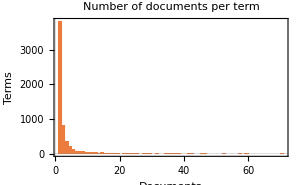
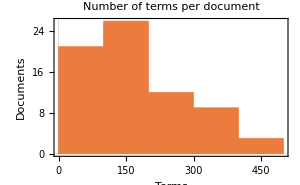
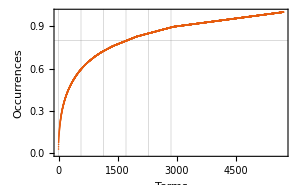
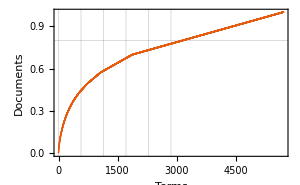
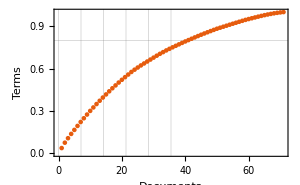
Context value "documentTermMatrix":  Dimensions:{71,5698} | Density:0.0314541 | 
-Graphics- | -Graphics- | Number of
documents per term
summary
{1 # documents
1st Qu | 1
Median | 1
Min | 1
3rd Qu | 2
Mean | 2.23324
Max | 70}
-Graphics- | -Graphics- | -Graphics-

{1.21207,Null}

```mathematica
AbsoluteTiming[
lsaRakuGuide=
LSAMonUnit[aDocs]⟹
LSAMonMakeDocumentTermMatrix[{},Automatic]⟹
LSAMonEchoDocumentTermMatrixStatistics["ParetoPrinciplePlots"->True,PlotTheme->"Scientific"]⟹
LSAMonApplyTermWeightFunctions["IDF","None","Cosine"];
]
```

### Извлечение темы

```mathematica
AbsoluteTiming[
lsaRakuGuide=
lsaRakuGuide⟹
LSAMonExtractTopics["NumberOfTopics"->60,"MinNumberOfDocumentsPerTerm"->1,Method->"NNMF",MaxSteps->12];
]
```

{2.33507,Null}

```mathematica
lsaRakuGuide⟹
LSAMonEchoTopicsTable["NumberOfTableColumns"->8,"NumberOfTerms"->20];
```

topics table:  1
1.000 | chart
0.757 | bar
0.636 | sales
0.619 | plot
0.501 | line
0.462 | forecast
0.460 | $actual
0.402 | 10]
0.402 | [10
0.389 | barras
0.383 | values
0.343 | graf
0.314 | combo
0.310 | dibujar
0.285 | líneas
0.253 | actual
0.226 | ventas
0.226 | previsión
0.226 | role
0.217 | method | 9
1.000 | $age
0.530 | $name
0.500 | $edad
0.349 | doe
0.328 | //docs
0.314 | note
0.275 | https
0.265 | $nombre
0.252 | org/type/str
0.252 | org/type/rat
0.252 | org/type/int
0.252 | numerator
0.252 | nude
0.252 | denominator
0.252 | chars
0.252 | applicable
0.252 | применяемых
0.223 | flip
0.223 | списком
0.223 | полным | 17
1.000 | star
0.996 | rakudo
0.769 | //rakudo
0.769 | pwd
0.769 | docker
0.571 | install
0.384 | tar
0.384 | instalación
0.384 | bashrc
0.286 | linux
0.284 | https
0.192 | \$path
0.192 | xzf
0.192 | sudo
0.192 | /share/perl6/vendor/bin
0.192 | /share/perl6/site/bin
0.192 | /share/perl6/core/bin
0.192 | \rakudo\bin
0.192 | ~/rakudo
0.192 | pull | 25
1.000 | 1|2|3
0.500 | junction
0.500 | ensamblaje
0.500 | скрещение
0.495 | $var
0.333 | junctions
0.333 | ensamblajes
0.333 | *autothreading*
0.191 | variable
0.167 | usually
0.167 | triggers
0.167 | superposition
0.167 | superposición
0.167 | logical
0.167 | *junction*
0.167 | *ensamblaje*
0.167 | combinan
0.167 | carried
0.167 | *автоматический
0.167 | суперпозиция | 33
1.000 | $var
0.942 | @numbers
0.752 | 123
0.605 | 999
0.605 | 99]
0.471 | @números
0.379 | array
0.369 | variables
0.336 | estado
0.325 | push
0.272 | sort
0.269 | state
0.269 | binding
0.269 | состояние
0.248 | int
0.217 | perl6
0.202 | vinculación
0.202 | =sort
0.202 | org/language/variables
0.202 | mutators | 41
1.000 | map
0.639 | squared
0.368 | @array
0.274 | cuadrado
0.259 | argument
0.258 | array
0.226 | &squared
0.226 | citizens
0.226 | высшего
0.199 | función
0.198 | function
0.193 | argumento
0.182 | primera
0.181 | toma
0.169 | они
0.168 | объекты
0.168 | orden
0.166 | аргумент
0.160 | subroutine
0.159 | subrutina | 49
1.000 | repl
0.826 | [enter]
0.360 | line
0.358 | rakudo
0.340 | línea
0.302 | perl6
0.279 | zef
0.271 | linux
0.263 | install
0.263 | print
0.252 | star
0.199 | código
0.189 | строки
0.188 | readline
0.188 | _readline_
0.188 | linenoise
0.188 | exit
0.188 | eval
0.186 | кода
0.173 | terminal | 57
1.000 | constructor
0.828 | \=>
0.789 | $lazylist
0.625 | конструктор
0.623 | $sex
0.623 | $nationality
0.490 | new
0.467 | $age
0.439 | age
0.395 | $listaperezosa
0.362 | generador
0.356 | $john
0.335 | provided
0.325 | generator
0.325 | bless
0.320 | lazy
0.311 | $sexo
0.311 | $nacionalidad
0.311 | arguments*
0.311 | *argumentos
2
1.000 | age
0.652 | $john
0.500 | edad
0.378 | sayvar
0.326 | $juan
0.313 | atributo
0.267 | human
0.254 | readonly
0.240 | acceso
0.234 | class
0.219 | $var
0.214 | access
0.182 | доступа
0.177 | attribute
0.177 | private
0.176 | attributes
0.176 | atributos
0.168 | инкапсуляция
0.165 | method
0.164 | объекта | 10
1.000 | alien
0.592 | greeting
0.456 | sub
0.333 | *subs*
0.333 | earthlings
0.295 | определение
0.289 | definition
0.269 | saludo
0.269 | определения
0.193 | definición
0.167 | terrícolas
0.167 | *subrutinas*
0.167 | *subroutines*
0.167 | reusing
0.167 | *functions*
0.167 | *funciones*
0.167 | denominadas
0.167 | begins
0.167 | *подпрограммы*
0.167 | *функциями* | 18
1.000 | txt
1.000 | spurt
1.000 | slurp
0.444 | $newdata
0.444 | $datos
0.444 | $data
0.444 | nuevos
0.444 | datafile
0.361 | file
0.344 | ====
0.340 | datos
0.333 | txt_
0.333 | scores
0.333 | paulo
0.308 | archivo
0.248 | файл
0.222 | puntuaciones
0.222 | paulie
0.222 | newdatafile
0.222 | _newdatafile | 26
1.000 | greet
0.824 | multi
0.564 | $title
0.560 | $name
0.501 | morning
0.452 | saludo
0.392 | good
0.375 | laura
0.282 | $título
0.282 | mrs
0.280 | $nombre
0.250 | johnnie
0.228 | días
0.228 | buenos
0.227 | подпрограмм
0.186 | sub
0.182 | normal
0.155 | subrutinas
0.155 | multiple
0.141 | subs | 34
1.000 | $var2
0.200 | nil
0.123 | int
0.122 | variable
0.087 | tipo
0.086 | $var
0.081 | bool
0.080 | type
0.067 | strongly
0.067 | estática
0.063 | true
0.062 | переменной
0.059 | introspection
0.059 | интроспекция
0.059 | introspección
0.059 | empty
0.058 | declarada
0.056 | declared
0.055 | тип
0.050 | valor | 42
1.000 | |===
0.864 | operandos
0.864 | 666667
0.599 | options=
0.599 | header
0.599 | [cols=
0.576 | reversed
0.576 | intercambio
0.301 | operator
0.288 | reversing
0.288 | operands
0.288 | intercambien
0.288 | delante
0.288 | adding
0.288 | добавление
0.288 | операнды
0.288 | обратный
0.288 | обратные
0.288 | меняет
0.288 | любым | 50
1.000 | int32
0.530 | add
0.471 | int
0.402 | ncitest
0.398 | libpath
0.333 | suma
0.199 | $*cwd/ncitest
0.185 | constant
0.183 | nativecall
0.170 | native
0.167 | целых
0.167 | enteros
0.167 | integers
0.164 | return
0.151 | числа
0.122 | функция
0.122 | sub
0.120 | simple
0.101 | raku
0.094 | repeat | 58
1.000 | class
0.869 | human
0.793 | sex
0.793 | nationality
0.648 | new
0.619 | |===
0.566 | $john
0.536 | people
0.536 | человека
0.529 | sexo
0.529 | nacionalidad
0.509 | age
0.487 | humano
0.486 | класса
0.399 | clase
0.392 | variables
0.357 | oriented_
0.357 | objetos_
0.357 | *objetos*
0.357 | *objects*
3
1.000 | symbol
0.979 | libpath
0.806 | ncitest
0.745 | char*
0.708 | hellofromc
0.581 | native
0.520 | hello
0.489 | $*cwd/ncitest
0.456 | nativecall
0.455 | constant
0.439 | str
0.373 | void
0.373 | <stdio
0.373 | printf
0.373 | #include
0.354 | holadesdec
0.318 | función
0.316 | raku
0.292 | sub
0.248 | modified | 11
1.000 | world
0.604 | hello
0.571 | mundo
0.413 | ritual
0.248 | hola
0.206 | comenzamos
0.206 | ритуала
0.206 | стоит
0.206 | мир
0.183 | shall
0.183 | begin
0.183 | привет
0.167 | ¡hola
0.166 | начать
0.153 | написать
0.143 | ещё
0.134 | escribirse
0.119 | written
0.098 | нам
0.090 | так | 19
1.000 | md5
0.429 | digest
0.286 | md5_hex
0.253 | wikipedia
0.212 | unicode
0.190 | $password
0.190 | $hashed
0.190 | $contraseña
0.190 | password
0.190 | cifrado
0.168 | hash
0.143 | utf
0.143 | [https
0.143 | encoding
0.143 | 128
0.141 | install
0.106 | módulo
0.106 | модуль
0.106 | link
0.105 | zef | 27
1.000 | unicmp
0.692 | sort
0.667 | //unicode
0.667 | collate
0.667 | =====
0.591 | cmp
0.536 | http
0.504 | números
0.495 | link
0.444 | org/reports/tr10/[unicode
0.444 | collation
0.444 | algorithm]
0.341 | ====
0.333 | numerals
0.331 | unicode
0.248 | operadores
0.222 | unicode]
0.222 | sorting
0.222 | org/reports/tr10/[algoritmo
0.222 | ordenar | 35
1.000 | regex
0.746 | l>+
0.700 | email
0.497 | $email
0.400 | valid
0.373 | org
0.373 | n>+
0.331 | <many
0.293 | letters
0.249 | $regex
0.249 | letters>
0.249 | [dot]
0.249 | doe@perl6
0.249 | совпадает
0.200 | matches
0.184 | válido
0.177 | coincide
0.166 | <varias
0.166 | <dot>
0.166 | *[dot]* | 43
1.000 | $number
1.000 | seats
0.983 | $age
0.873 | elsif
0.667 | asientos
0.666 | condition
0.587 | welcome
0.547 | else
0.532 | condición
0.500 | $número
0.500 | sedan
0.491 | $edad
0.367 | условие
0.333 | seater
0.319 | true
0.295 | van
0.294 | bienvenido
0.291 | met
0.291 | cumple
0.269 | evalúa | 51
1.000 | squared
0.532 | return
0.468 | int
0.445 | cuadrado
0.417 | retorno
0.314 | equal
0.268 | sub
0.221 | ====
0.187 | type
0.156 | value
0.142 | tipo
0.141 | org/language/functions
0.141 | возвращаемого
0.141 | возвращаемое
0.139 | valor
0.128 | тип
0.125 | возврат
0.125 | указывать
0.115 | igual
0.114 | failed | 59
1.000 | ncitest
0.902 | gcc
0.448 | libpath
0.421 | hellofromc
0.361 | shared
0.361 | libncitest
0.299 | native
0.214 | library
0.210 | holadesdec
0.209 | nativecall
0.180 | $*cwd
0.180 | fpic
0.180 | dynamiclib
0.180 | dylib
0.180 | dll
0.180 | c\n
0.169 | librería
0.145 | macos
0.134 | linux
0.127 | function
4
1.000 | catch
0.676 | exceptions
0.476 | excepciones
0.458 | adhoc
0.442 | hoc
0.371 | исключения
0.370 | today
0.361 | $name
0.348 | enlightenment
0.330 | exception
0.330 | try
0.319 | light
0.302 | str
0.295 | die
0.288 | excepción
0.256 | block
0.230 | goes
0.209 | algo
0.208 | исключений
0.197 | lanza | 12
1.000 | %capitals
0.627 | france
0.556 | germany
0.556 | london
0.555 | berlin
0.501 | paris
0.501 | keys
0.500 | %capitales
0.444 | hash
0.333 | capital
0.313 | londres
0.313 | francia
0.303 | push
0.278 | alemania
0.278 | berlín
0.251 | parís
0.233 | hashes
0.201 | values
0.188 | org/type/hash
0.188 | key | 20
1.000 | 120
0.732 | variables
0.579 | |===
0.500 | reduction
0.500 | reducción
0.500 | org/language/operators
0.500 | свёртки
0.500 | [+]
0.500 | [*]
0.496 | hashes
0.495 | operadores
0.461 | arrays
0.372 | operators
0.346 | переменные
0.346 | options=
0.346 | header
0.346 | [cols=
0.317 | используется
0.295 | scalars
0.295 | escalares | 28
1.000 | @final
0.902 | <==
0.902 | ==>
0.646 | array
0.617 | @array
0.533 | reverse
0.451 | hacia
0.424 | unique
0.376 | feed
0.362 | sort
0.301 | alimentación
0.226 | лента
0.150 | step
0.150 | paso
0.150 | forward
0.150 | backward
0.150 | atrás
0.150 | arriba
0.150 | abajo
0.150 | прямая | 36
1.000 | match
0.747 | else
0.679 | coincide
0.548 | a+z
0.548 | a*z
0.274 | aaz
0.274 | aaaaaaaaaaz
0.183 | repite
0.153 | say
0.147 | раз
0.126 | vez
0.102 | significa
0.095 | означает
0.091 | times
0.091 | quantifiers
0.091 | ninguna
0.091 | cuantificadores
0.091 | кванторы
0.089 | means
0.081 | zero | 44
1.000 | 2+|
0.842 | link
0.752 | long
0.564 | unsigned
0.510 | https
0.376 | size_t
0.376 | short
0.376 | char
0.349 | int
0.313 | irc
0.303 | bool
0.295 | int32
0.253 | double
0.251 | reddit
0.215 | raku
0.203 | |===
0.188 | //web
0.188 | uint8_t
0.188 | uint8
0.188 | uint64_t | 52
1.000 | $jane
0.866 | ^methods
0.866 | ^attributes
0.853 | self
0.578 | ^parents
0.543 | human
0.500 | $juana
0.449 | employee
0.442 | $john
0.435 | method
0.425 | company
0.380 | object
0.374 | age
0.357 | objeto
0.322 | name
0.302 | str
0.297 | class
0.289 | _true_
0.289 | {say
0.289 | org/language/objects | 60
1.000 | employee
0.761 | human
0.744 | class
0.697 | introduce
0.632 | company
0.596 | age
0.560 | salary
0.475 | empleado
0.424 | name
0.384 | preséntate
0.340 | humano
0.339 | compañía
0.331 | edad
0.304 | self
0.303 | salario
0.273 | $jane
0.271 | acme
0.271 | 4000
0.260 | classes
0.252 | ====
5
1.000 | m/light/
0.545 | regex
0.500 | rx/light/
0.500 | m/ilumina/
0.476 | light
0.443 | /light/
0.418 | regular
0.281 | blanco
0.270 | пробела
0.270 | espacio
0.250 | white
0.250 | space
0.250 | rx/ilumina/
0.250 | indique
0.250 | ignorado
0.250 | регулярного
0.250 | указано
0.241 | игнорируются
0.238 | ilumina
0.227 | match | 13
1.000 | zoo
0.786 | @animals
0.537 | array
0.536 | vicuña
0.500 | owl
0.470 | arrays
0.445 | llama
0.443 | camel
0.429 | @array[3]
0.429 | animal
0.393 | @animales
0.286 | animals
0.286 | animales
0.250 | búho
0.238 | массив
0.222 | camello
0.214 | @tbl[3
0.214 | @tbl[2
0.214 | @tbl[1
0.214 | @tbl[0 | 21
1.000 | *zef*
1.000 | test
1.000 | suite
1.000 | star*
1.000 | *rakudo*
1.000 | *rakudo
1.000 | *raku*
0.858 | rakudo
0.737 | zef
0.667 | specification
0.667 | pruebas
0.667 | especificación
0.667 | banco
0.667 | менеджер
0.537 | модулей
0.537 | módulos
0.462 | raku
0.333 | *rakudobrew*
0.333 | jargon
0.333 | includes | 29
1.000 | 2+|
0.798 | true
0.752 | 3+|
0.687 | infix
0.687 | инфиксный
0.545 | infijo
0.522 | false
0.436 | $var
0.376 | footnote
0.248 | constructor
0.226 | {vbar}
0.226 | <m|
0.226 | 6+|
0.226 | 5+|
0.222 | range
0.203 | numeric
0.201 | leg
0.201 | intervals[]
0.178 | префиксный
0.162 | prefix | 37
1.000 | script123
0.739 | carpeta
0.667 | folder123
0.500 | rmdir
0.494 | directory
0.469 | директории
0.443 | mkdir
0.434 | dir
0.368 | carpetas
0.333 | newfolder
0.333 | carpeta123
0.295 | empty
0.250 | /rakudo/bin
0.250 | \\rakudo\\bin
0.250 | org/type/io
0.250 | directories
0.222 | ruta
0.222 | путь
0.222 | vacía
0.221 | checks | 45
1.000 | map
0.912 | {$x
0.608 | $squared
0.608 | anonymous
0.495 | @array
0.456 | anónima
0.304 | $cuadrado
0.304 | pointy
0.304 | *lambda*
0.259 | función
0.225 | entrada
0.210 | block
0.207 | functions
0.194 | funciones
0.194 | функцию
0.171 | function
0.164 | variables
0.152 | vinculada
0.152 | referimos
0.152 | *pointy | 53
1.000 | $var
0.454 | variable
0.401 | accesible
0.372 | bloque
0.355 | видимости
0.346 | block
0.323 | accessible
0.312 | str
0.261 | $var=1
0.220 | text
0.200 | объявлена
0.200 | достижима
0.200 | блоке
0.195 | 123
0.178 | области
0.178 | alcance
0.178 | declaración
0.178 | область
0.161 | блока
0.137 | переменная | 
6
1.000 | else
0.973 | contains
0.897 | unicode
0.786 | contain
0.785 | contiene
0.716 | dash
0.702 | doesn
0.606 | pd>
0.606 | lu>
0.606 | devanagari
0.606 | ascii
0.606 | свойства
0.606 | иван
0.606 | १२३
0.601 | letter
0.537 | привет
0.537 | propiedades
0.537 | properties
0.487 | юникода
0.404 | uppercase | 14
1.000 | item
0.900 | $array
0.329 | @array
0.300 | 100
0.300 | *100
0.116 | array
0.100 | iterates
0.100 | itera
0.100 | осуществили
0.100 | цикла
0.089 | каждым
0.089 | creado
0.089 | iteration
0.089 | iteración
0.089 | операцию
0.089 | обходит
0.089 | создали
0.089 | обратите
0.089 | observa
0.089 | serie | 22
1.000 | org/language/concurrency
0.917 | nativecall
0.886 | interfaz
0.667 | интерфейс
0.591 | concurrency
0.591 | concurrencia
0.591 | interface
0.591 | нативных
0.537 | llamadas
0.537 | вызовов
0.537 | nativas
0.495 | calling
0.462 | raku
0.435 | //docs
0.425 | native
0.413 | note
0.394 | https
0.366 | узнать
0.333 | ships
0.333 | ofrece | 30
1.000 | small
1.000 | nfd
1.000 | nfc
0.826 | letter
0.667 | \x00e1
0.667 | \x0061\x0301
0.667 | uniname
0.667 | \c[latin
0.660 | unicode
0.538 | символа
0.537 | point
0.444 | acute
0.355 | código
0.340 | code
0.333 | $δ++
0.333 | \x263a
0.333 | \x0061
0.333 | smiling
0.333 | face]
0.333 | \c[white | 38
1.000 | given
0.722 | proceed}
0.698 | $var
0.490 | int
0.482 | huh
0.401 | default
0.361 | switch
0.361 | proceed
0.356 | equal
0.241 | ¿ejem
0.241 | успешного
0.222 | match
0.221 | successful
0.202 | matching
0.194 | coincidencia
0.167 | entero
0.167 | первого
0.165 | say
0.149 | menos
0.140 | igual | 46
1.000 | whitespace
0.833 | caracter
0.803 | except
0.773 | любой
0.741 | кроме
0.736 | blanco
0.728 | символ
0.647 | menos
0.623 | horizontal
0.610 | character
0.599 | espacio
0.498 | *regex*
0.434 | cualquier
0.433 | |===
0.395 | valid
0.381 | else
0.374 | vertical
0.374 | dígito
0.374 | digit
0.331 | пробел | 54
1.000 | greeting
0.573 | generator
0.560 | $period
0.431 | morning
0.415 | saludo
0.408 | $morning
0.408 | $generated
0.408 | $evening
0.336 | good
0.306 | $momento
0.306 | evening
0.236 | sub
0.226 | creado
0.225 | subroutine
0.221 | $name
0.213 | crear
0.212 | doe
0.204 | return
0.204 | $tardes
0.204 | $saludo | 
7
1.000 | https
0.762 | //www
0.738 | //atom
0.615 | vim
0.615 | highlighting
0.593 | syntax
0.545 | enabled
0.436 | editor
0.434 | sintaxis
0.412 | //github
0.396 | http
0.369 | perl6[perl
0.369 | org/[vim]
0.369 | io/packages/language
0.369 | io/[atom]
0.369 | gnu
0.369 | fe]
0.307 | //raku
0.246 | visualstudio
0.246 | visualización | 15
1.000 | shell
0.360 | echo
0.240 | dir
0.187 | windows
0.185 | run
0.160 | оболочки
0.145 | командной
0.135 | neo
0.135 | linux/macos
0.134 | linux
0.110 | ejecuta
0.109 | команду
0.090 | equivalente
0.090 | запускает
0.089 | $name
0.080 | comando
0.080 | пользуетесь
0.080 | equivalent
0.080 | эквивалент
0.073 | выводит | 23
1.000 | @final
0.869 | array
0.774 | @array
0.758 | unique
0.750 | reverse
0.586 | sort
0.282 | chained
0.250 | encadenamiento
0.227 | pass
0.188 | сцепление
0.188 | передаём
0.167 | chaining
0.166 | pasamos
0.140 | методов
0.138 | аргумент
0.134 | result
0.123 | результат
0.123 | methods
0.122 | массива
0.117 | resultado | 31
1.000 | match
0.684 | abc
0.684 | a2c
0.678 | coincide
0.456 | wildcards
0.456 | comodines
0.456 | подстановки
0.437 | символ
0.376 | else
0.315 | regex
0.228 | wildcard
0.228 | точка
0.202 | выражениях
0.202 | dot
0.195 | любой
0.184 | регулярных
0.169 | significa
0.158 | означает
0.156 | say
0.148 | means | 39
1.000 | hello
0.905 | paula
0.588 | $name
0.552 | подпрограмма
0.535 | signatura
0.535 | paul
0.470 | str
0.445 | input
0.428 | subrutina
0.428 | subroutine
0.408 | sub
0.359 | hola
0.348 | definir
0.302 | ¡¡hola
0.302 | requerir
0.302 | *parámetros*
0.302 | *parameters*
0.302 | ninguno
0.302 | ésta
0.302 | подпрограммой | 47
1.000 | var
0.705 | loop
0.667 | comment
0.600 | var1
0.544 | hello
0.533 | comentario
0.508 | world
0.459 | |===
0.400 | 1+2
0.400 | комментарий
0.293 | ====
0.267 | término
0.267 | term
0.261 | hola
0.243 | case
0.237 | $name
0.234 | quotes
0.231 | mundo
0.219 | $i++
0.219 | org/language/control | 55
1.000 | prime
0.590 | map
0.555 | race
0.476 | {is
0.396 | @array2
0.396 | @array1
0.352 | @array
0.317 | @result
0.317 | init
0.317 | await
0.314 | hello
0.273 | hyper
0.256 | start
0.253 | array
0.231 | laura
0.211 | @result2
0.211 | @result1
0.164 | ====
0.159 | {$_
0.159 | @resultado | 
8
1.000 | human
0.711 | counter
0.562 | class
0.500 | humano
0.491 | bless
0.488 | new
0.429 | $name
0.363 | self
0.355 | counter++
0.355 | contador
0.344 | clase
0.325 | атрибуты
0.307 | atributos
0.307 | attributes
0.300 | класса
0.223 | objects
0.223 | method
0.214 | $nombre
0.213 | sus
0.185 | lugar | 16
1.000 | tmtowtdi
0.667 | toady
0.667 | tim
0.495 | general
0.461 | raku
0.386 | way
0.333 | supports
0.333 | soporta
0.333 | pronunciado
0.333 | pronounced
0.333 | procedural
0.333 | procedimental
0.333 | paradigmatic
0.333 | nivel
0.333 | multiparadigma
0.333 | motto
0.333 | level
0.333 | lema
0.333 | high
0.333 | gradually | 24
1.000 | shoes
0.927 | unless
0.667 | $clean
0.500 | zapatos
0.372 | false
0.333 | $limpiar
0.333 | clean
0.167 | limpia
0.148 | tus
0.138 | else
0.133 | condition
0.133 | condición
0.133 | negación
0.123 | условие
0.097 | written
0.083 | claúsula
0.083 | clause
0.083 | противоположность
0.083 | осуществляется
0.083 | логическое | 32
1.000 | print
0.895 | prompt
0.703 | ====
0.561 | $name
0.449 | dear
0.398 | welcome
0.388 | terminal
0.295 | [enter]
0.280 | $nombre
0.274 | строки
0.224 | ¿que
0.224 | ¿cual
0.224 | sir
0.224 | mam
0.199 | bienvenido
0.199 | ввода
0.199 | tal
0.178 | ¡hola
0.178 | hello
0.169 | say | 40
1.000 | orwith
0.722 | $var
0.444 | elsif
0.431 | $var=1
0.412 | int
0.381 | hello
0.372 | unless
0.333 | сравнить
0.238 | variable
0.183 | hola
0.167 | relate
0.167 | parecidos
0.167 | parecido
0.167 | противоположностью
0.167 | альтернативную
0.167 | конструкцию
0.167 | определена
0.167 | ничего
0.167 | ветка
0.167 | эту | 48
1.000 | @array>>
0.945 | prime
0.667 | &is
0.667 | hiperoperador
0.520 | //raku
0.500 | 10>
0.446 | hyper
0.443 | например
0.443 | par
0.422 | $var
0.413 | lista
0.384 | call
0.375 | list
0.372 | print
0.361 | perl
0.346 | warning
0.333 | &es
0.333 | оригинальном
0.333 | результатов
0.333 | вызовет | 56
1.000 | $var
0.485 | str
0.416 | int
0.266 | @multilingual
0.266 | %country
0.266 | cool
0.266 | codes
0.266 | ^1m
0.236 | flip
0.218 | %capitals
0.216 | @array
0.157 | tipado
0.157 | type
0.151 | |===
0.148 | germany
0.142 | failed
0.141 | variable
0.133 | salut
0.133 | país
0.133 | noen |

### Извлечение статистического тезауруса

```mathematica
lsaRakuGuide⟹
LSAMonEchoStatisticalThesaurus["Words"->{"regex","interface","expression","operator","object","programming","read","recommended","variable","tmtowtdi"}];
```

statistical thesaurus:  term | statistical thesaurus entries
expression | {expression,expresión,выражение,así,выражения,/ilumina/,игнорируются,explicitly,ignored,explícita,явно,указано}
interface | {нативных,interface,nativas,интерфейс,calling,concurrencia,concurrency,вызовов,llamadas,упростить,асинхронности,взаимодействие}
object | {object,objeto,объекта,методы,eligible,private,adulto,метод,assess,eligibility,twigil,encapsulación}
operator | {operator,оператор,обычная,операторов,перед,operador,операторы,operación,original,результат,любым,меняет}
programming | {programming,programación,más,info,больше,información,funcional,functional,программирование,hay,orientada,есть}
read | {read,running,сохранять,напечатать,рекомендуется,aparecerá,flechas,hitting,recommended,window,eval,exit}
recommended | {сохранять,напечатать,рекомендуется,aparecerá,flechas,hitting,recommended,window,estas,eval,exit,linenoise}
regex | {regex,l>+,email,$email,n>+,org,<many,valid,letters,совпадает,doe@perl6,[dot]}
tmtowtdi | {tmtowtdi,tim,toady,general,way,тим,девиз,тоуди,уровня,простые,сложные,сложным}
variable | {variable,accesible,видимости,accessible,$var=1,text,bloque,переменной,переменная,блоке,достижима,объявлена}

## Деконструкция коллекции случайных мандал

"Comparison of dimension reduction algorithms over mandala images generation"

"LSA methods comparison over random mandalas deconstruction -- WL"

"LSA methods comparison over random mandalas deconstruction -- Python"

"Re-exploring the structure of Chinese character images"

## Изготовление маски Роршаха (из фильма "Watchmen" 2009)

"Rorschach mask animations projected over 3D surfaces"

"Details in Rorschach mask animations making"

## Ссылки

### Articles

[AA1] Anton Antonov, A monad for Latent Semantic Analysis workflows, (2019), MathematicaForPrediction at GitHub.

### Packages and paclets

[AA2] Anton Antonov, Monadic Latent Semantic Analysis Mathematica package, (2017), MathematicaForPrediction at GitHub.
    URL: https://github.com/antononcube/MathematicaForPrediction/blob/master/MonadicProgramming/MonadicLatentSemanticAnalysis.m .

### Videos

[AAv1] Anton Antonov, "Making of Rorschach mask 2D and 3D animations", (2022), YouTube/@AAA4Prediction.

## Setup

### Install paclets

```mathematica
PacletInstall["AntonAntonov/MonadMakers"]
```

PacletObject[…]

```mathematica
PacletInstall["AntonAntonov/MonadicLatentSemanticAnalysis"]
```

PacletObject[…]

```mathematica
PacletInstall["AntonAntonov/DimensionReducers"]
```

PacletObject[…]

```mathematica
PacletInstall["AntonAntonov/DataReshapers"]
```

PacletObject[…]

### Load paclets

```mathematica
Needs["AntonAntonov`MonadicLatentSemanticAnalysis`"]
Needs["AntonAntonov`DimensionReducers`"]
Needs["AntonAntonov`DataReshapers`"]
```

### Raku manuals

```mathematica
aDocs=;
```